```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
Clear[partpath,impVoltages,impLatticesites,impCurrents];
partpath="C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\Desktop\\Used Data\\PBC Hermitian\\Stromstabilisiert\\6 Boards";
(*dir="Input unit cell 4,4,4 1 Vpp after resoldering, 2_43MHz 01";*)
dir="\\Input unit cell (4,1,3), 2_4MHz, current stabilized 8.53mArms to less than 0.25% (22.05.02)";

impVoltages=Import[partpath<>dir<>"\\2D_Measurement_01*.dat",HeaderLines->1];
impLatticesites=Import[partpath<>dir<>"\\2D_Measurement_02*.dat",HeaderLines->1];
impCurrents=Import[partpath<>dir<>"\\Current\\2D_Measurement_01*.dat",HeaderLines->1];
(*
impVoltages=Import["G:\\GitHub\eti\\Data\\PBC hermitian\\Input unit cell 4,4,4 1Vpp\\2D_Measurement_01*.dat",HeaderLines->1];
impLatticesites=Import["G:\\GitHub\\eti\\Data\\PBC hermitian\\Input unit cell 4,4,4 1Vpp\\2D_Measurement_02*.dat",HeaderLines->1];
impCurrents=Import["G:\\GitHub\\eti\\Data\\PBC hermitian\\Input unit cell 4,4,4 1Vpp\\Current\\2D_Measurement_01*.dat",HeaderLines->1];
*)
NUnit=8;
NVertical=6;
Frequency = 2.4*10^6;
```

### Position of current input:

```mathematica
{x,y,z}={4,1,3};
meanVoltages=Map[Mean,Partition[#,100]&/@impVoltages,{2}];
MinMax[Flatten[meanVoltages[[All,All,4]]]];
sortedLatticeSites=(SortBy[#,#[[1]]]&/@impLatticesites);(*Voltage data sorted by increasing Lock-In number -> sort LatticeSites in the same way*)
(*[[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
(*
new=Table[If[meanVoltages[[measurement,device,4]]<10.0*10^-3,{meanVoltages[[measurement,device,1]],0.,0.,0.,0.},meanVoltages[[measurement,device]]],{measurement,1,Length[meanVoltages]},{device,1,4}];

meanVoltages=new;
*)
```

```mathematica
(*
lstTochange1=meanVoltages[[1;;256,All,4]];
newList1=0.00255/guessAmplitude[[1;;256]]*lstTochange1;
lstTochange2=meanVoltages[[256+1;;256+256,All,4]];
newList2=0.002375/guessAmplitude[[256+1;;256+256]]*lstTochange2;
meanVoltages[[All,All,4]]=Join[newList1,newList2];
*)
```

```mathematica
data=Table[Flatten[{meanVoltages[[m,q,2]]+ⅈ meanVoltages[[m,q,3]],sortedLatticeSites[[m,q,2;;4]],sortedLatticeSites[[m,q,8]]}],{m,1,Dimensions[impVoltages][[1]]},{q,1,4}];
```

```mathematica
(*Split by measurement 1 and 2 -> [[Input 1/2],[Measurements],[Lock-Ins],[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
data=Partition[data,(Dimensions[data][[1]])/2];
(*Split into inputs sorted by sublattice sites ->[[SublatticeA/B], [Measurements with all Lock-Ins],[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
input1=Partition[SortBy[Flatten[data[[1]],1],#[[5]]&],(Dimensions[data][[2]]*Dimensions[data][[3]])/2];
input2=Partition[SortBy[Flatten[data[[2]],1],#[[5]]&],(Dimensions[data][[2]]*Dimensions[data][[3]])/2];
(*Sort all inputs by unit cells -> 1,1,1, 2,1,1, ... 7,8,8, 8,8,8*)
sortedInput1First=SortBy[input1[[1]],(#[[4]]*100+#[[3]]*10+#[[2]])&];
sortedInput1Second=SortBy[input1[[2]],(#[[4]]*100+#[[3]]*10+#[[2]])&];
sortedInput1=Partition[Flatten[{sortedInput1First,sortedInput1Second},1],Length[sortedInput1First]];
sortedInput2First=SortBy[input2[[1]],(#[[4]]*100+#[[3]]*10+#[[2]])&];
sortedInput2Second=SortBy[input2[[2]],(#[[4]]*100+#[[3]]*10+#[[2]])&];
sortedInput2=Partition[Flatten[{sortedInput2First,sortedInput2Second},1],Length[sortedInput2First]];
(*[[Input1/2],[SublatticeSite1/2],[SortedMeasurements],[Voltage,DimX1,DimX2,DimX3,Sublattice]]*)
sortedInput={sortedInput1,sortedInput2};
shuntresistor=20.;

currentData=(#[[2]]+ⅈ #[[3]])/shuntresistor&/@Flatten[Map[Mean,Partition[#,100]&/@impCurrents,{2}],1];
```

```mathematica
(* z-index reversed to achieve right handed coordinates *)
```

```mathematica
(*
currentData={(0.00255*#)/Abs[#]&@currentData[[1]],(0.002375*#)/Abs[#]&@currentData[[1]]};
*)

(*
sortedCurrentInput={{Table[{currentData[[1]]*KroneckerDelta[((NUnit-(z-1)-1)*NUnit^2)+((y-1)*NUnit)+x,q]},{q,1,512}],
Table[{0},{512}]},{Table[{0},{512}],Table[{currentData[[2]]*KroneckerDelta[((NUnit-(z-1)-1)*NUnit^2)+((y-1)*NUnit)+x,q]},{q,1,512}]}};
*)

sortedCurrentInput={{Table[{currentData[[1]]*KroneckerDelta[((z-1)*NUnit^2)+((y-1)*NUnit)+x,q]},{q,1,Length[sortedInput1First]}],
Table[{0},{Length[sortedInput1First]}]},{Table[{0},{Length[sortedInput1First]}],Table[{currentData[[2]]*KroneckerDelta[((z-1)*NUnit^2)+((y-1)*NUnit)+x,q]},{q,1,Length[sortedInput1First]}]}};
```

```mathematica
Vak[i_,kx_,ky_,kz_]:=∑_(k=1)^NVertical (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedInput[[i,1,((k-1)*NUnit^2)+((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*(j-1)/NUnit])*Exp[-ⅈ*2*π*ky*(l-1)/NUnit])*Exp[-ⅈ*2*π*kz*(k-1)/NVertical];
Vbk[i_,kx_,ky_,kz_]:=∑_(k=1)^NVertical (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedInput[[i,2,((k-1)*NUnit^2)+((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*(j-1)/NUnit])*Exp[-ⅈ*2*π*ky*(l-1)/NUnit])*Exp[-ⅈ*2*π*kz*(k-1)/NVertical];
Iak[i_,kx_,ky_,kz_]:=∑_(k=1)^NVertical (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedCurrentInput[[i,1,((k-1)*NUnit^2)+((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*(j-1)/NUnit])*Exp[-ⅈ*2*π*ky*(l-1)/NUnit])*Exp[-ⅈ*2*π*kz*(k-1)/NVertical];
Ibk[i_,kx_,ky_,kz_]:=∑_(k=1)^NVertical (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit sortedCurrentInput[[i,2,((k-1)*NUnit^2)+((l-1)*NUnit)+j,1]]*Exp[-ⅈ*2*π*kx*(j-1)/NUnit])*Exp[-ⅈ*2*π*ky*(l-1)/NUnit])*Exp[-ⅈ*2*π*kz*(k-1)/NVertical];
kList=Table[(k-1)*(2π/NUnit),{k,1,NUnit+1}];
kVerticalList = Table[(k-1)*(2π/NVertical),{k,1,NVertical+1}];
Clear[Lap,Detk];Detk[r_,s_,t_]:= (Vak[1,r,s,t]*Vbk[2,r,s,t])/(Iak[1,r,s,t]*Ibk[2,r,s,t])-(Vbk[1,r,s,t]*Vak[2,r,s,t])/(Iak[1,r,s,t]*Ibk[2,r,s,t]);
Lap[p_,q_,r_]:=(1/Detk[p,q,r])*{{Vbk[2,p,q,r]/Ibk[2,p,q,r],-Vak[2,p,q,r]/Ibk[2,p,q,r]},{-Vbk[1,p,q,r]/Iak[1,p,q,r],Vak[1,p,q,r]/Iak[1,p,q,r]}};
```

```mathematica
Clear[n1];
SetSharedVariable[n1];
n1=0;
Monitor[
resultPerMeasComplex=Parallelize[Table[
If[kz==1,n1++];
evals=Eigenvalues[Lap[kx-1,ky-1,kz-1]],{kx,1,NUnit},{ky,1,NUnit},{kz,1,NVertical}]];
(*resultPerCircuitComplex=Parallelize[Table[
If[kz==1,n1++];
evals=Eigenvalues[Lap[kx-1,ky-1,kz-1]],{kx,1,NUnit},{ky,1,NUnit},{kz,1,NUnit}]];*)
,Row[{"Step 1/1 ",ProgressIndicator[n1,{1,NUnit^2}]}]]

resultPerMeas=Table[SortBy[resultPerMeasComplex[[kx,ky,kz]],Im[#]&],{kx,1,NUnit},{ky,1,NUnit},{kz,1,NVertical}];
```

```mathematica
(*3D Plot of experimental data*)

(*,PlotRange->{-0.01,0.01}*)

resultPerTotMeas1=Range[NVertical];
resultPerTotMeas2=Range[NVertical];
resultPerTotMeas=Range[NVertical];
Do[
resultPerTotMeas1[[q]]=Flatten[Table[{kList[[i]],kList[[j]],Im[resultPerMeas[[If[i==NUnit+1,1,i],If[j==NUnit+1,1,j],q,1]]]},{i,1,NUnit},{j,1,NUnit}],1];
resultPerTotMeas2[[q]]=Flatten[Table[{kList[[i]],kList[[j]],Im[resultPerMeas[[If[i==NUnit+1,1,i],If[j==NUnit+1,1,j],q,2]]]},{i,1,NUnit},{j,1,NUnit}],1];
resultPerTotMeas[[q]]={resultPerTotMeas1[[q]],resultPerTotMeas2[[q]]};
,{q,1,NVertical,1}];
```

```mathematica
Omega = 2*π*Frequency;
LBZ = 27*10^-6;
L0A=5.6*10^-6;
L0B = 27*10^-6;
initialC = 150*10^-12;
C1 = Omega*150*10^-12;
CAz = C1;
Cy = C1/2;
alpha = -Omega/(Omega^2*L0A);
beta = -Omega/(Omega^2*L0B);
betaZ =  -Omega/(Omega^2*LBZ);
LBZControl = N[1/(Omega*LBZ)]

NTheory = 20;

kEVList=Table[(k-1)*(2π/NUnit),{k,1,NUnit}];
kEVVerticalList = Table[(k-1)*(2π/NVertical),{k,1,NVertical}];
```

0.00245609

```mathematica
Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]

Hc[{kx_,ky_,kz_}]:=N[(-(CAz+betaZ)Cos[ky]) X[0]-(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])) X[1]-C1 Sin[kz] X[2]-(CAz-betaZ) Cos[ky] X[3]]

(*Hc[{kx_,ky_,kz_}]:=N[{{2CAz+2C1+2Cy,0},{0,2C1+2Cy+2betaZ}}-{{2CAz*Cos[ky],C1+C1*Exp[-I*kz]+2Cy*Cos[ky-kx]},{C1+C1*Exp[I*kz]+2Cy*Cos[ky-kx],2betaZ*Cos[ky]}}+{{alpha,0},{0,beta}}]*)
```

```mathematica
HcEigenvals = Table[Eigenvalues[Hc[{kx,ky,kz}]],{kx,kEVList},{ky,kEVList},{kz,kEVVerticalList}];
```

```mathematica
range=Join[Range[1,37,9],Range[38,41,1],Range[32,5,-9],Range[4,1,-1]];
highsym=Flatten[Join[{resultPerTotMeas1[[1,#]],resultPerTotMeas2[[1,#]]}&/@range,{resultPerTotMeas1[[#,1]],resultPerTotMeas2[[#,1]]}&/@Range[2,NVertical/2],{resultPerTotMeas1[[NVertical/2+1,#]],resultPerTotMeas2[[NVertical/2+1,#]]}&/@range],1];
tmpRange=Flatten[Table[{m,m},{m,1,Length[highsym]}]];
ListPlot[Table[{tmpRange[[q]],highsym[[q,3]]},{q,1,Length[highsym]}],PlotLabel->"High symmetry path, Input: (7,8,3) @ 2,285 MHz",AxesLabel->{None,"Impedance [Ω]"},Ticks->{{{1,"Γ"}, {5,"X"},{9,"S"},{13,"Y"},{17,"Γ"},{20,"Z"}, {24,"U"},{28,"R"},{32,"T"},{36,"Z"}}, Automatic},PlotRange->{All,{-0.01,0.01}}];
```

Evaluation: High Symmetry Plot, Chern Number and Vector Field around Weyl Points

```mathematica
Omega = 2*π*Frequency;
LBZ = 27*10^-6;
L0A=5.6*10^-6;
L0B = 27*10^-6;
C1 = Omega*150*10^-12;
CAz = C1;
Cy = C1/2;
alpha = -Omega/(Omega^2*L0A);
beta = -Omega/(Omega^2*L0B);
betaZ =  -Omega/(Omega^2*LBZ);
LBZControl = 1/(Omega*LBZ);
```

```mathematica
Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]

Hc[{kx_,ky_,kz_}]:=N[(-(CAz+betaZ)Cos[ky]) X[0]-(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])) X[1]-C1 Sin[kz] X[2]-(CAz-betaZ) Cos[ky] X[3]]

(*Hc[{kx_,ky_,kz_}]:=N[{{2CAz+2C1+2Cy,0},{0,2C1+2Cy+2betaZ}}-{{2CAz*Cos[ky],C1+C1*Exp[-I*kz]+2Cy*Cos[ky-kx]},{C1+C1*Exp[I*kz]+2Cy*Cos[ky-kx],2betaZ*Cos[ky]}}+{{alpha,0},{0,beta}}]*)
```

```mathematica
Eigensystem[Lap[0,0,0]][[1]]
Ordering[Im[Eigensystem[Lap[0,0,0]][[1]]]]
```

{-0.00452139+0.0073224 ⅈ,0.00243454-0.00245376 ⅈ}

{2,1}

```mathematica
{0.00843515606612114,-0.007582868196449162}
```

{0.00843516,-0.00758287}

```mathematica
δ = 2π/NUnit;
δZ = 2π/NVertical;

kList=Table[(k-1)*(2π/NUnit),{k,1,NUnit}];
kZList=Table[(k-1)*(2π/NVertical),{k,1,NVertical}];

UTheory[Y_,Z_,{kx_,ky_,kz_}]:= Block[{
es1=Eigensystem[N[Hc[{kx,ky,kz}]]],
es2=Eigensystem[N[Hc[{kx,ky+Y*δ,kz+Z*δZ}]]]},
ev1=es1[[2,Ordering[es1[[1]]]]];
ev2=es2[[2,Ordering[es2[[1]]]]];
normEV1 = Table[Normalize[ev1[[i]]],{i,1,Length@ev1,1}];
normEV2 = Table[Normalize[ev2[[i]]],{i,1,Length@ev2,1}];
Table[(Conjugate[normEV1].Transpose[normEV2])[[i,i]],{i,1,Length@ev2,1}]
]

UExperiment[Y_,Z_,{kx_,ky_,kz_}]:= Block[{
es1=Eigensystem[N[Lap[kx*NUnit/(2π),ky*NUnit/(2π),kz*NVertical/(2π)]]],
es2=Eigensystem[N[Lap[kx*NUnit/(2π),(ky+Y*δ)*NUnit/(2π),(kz+Z*δZ)*NVertical/(2π)]]]},
ev1=es1[[2,Ordering[Im[es1[[1]]]]]];
ev2=es2[[2,Ordering[Im[es2[[1]]]]]];
normEV1 = Table[Normalize[ev1[[i]]],{i,1,Length@ev1,1}];
normEV2 = Table[Normalize[ev2[[i]]],{i,1,Length@ev2,1}];
Table[(Conjugate[normEV1].Transpose[normEV2])[[i,i]],{i,1,Length@ev2,1}]
]

BerryTheoryV2[kx_,ky_,kz_]:=Block[{
U1Kl=UTheory[1,0,{kx,ky,kz}],
U2Kl1=UTheory[0,1,{kx,ky+δ,kz}],
U1Kl2=UTheory[1,0,{kx,ky,kz+δZ}],
U2Kl=UTheory[0,1,{kx,ky,kz}]
},
Im@Table[Log[(U1Kl[[i]])(U2Kl1[[i]])((U1Kl2[[i]])^-1)((U2Kl[[i]])^-1)],{i,2}]
]

BerryExperimentV2[kx_,ky_,kz_]:=Block[{
U1Kl=UExperiment[1,0,{kx,ky,kz}],
U2Kl1=UExperiment[0,1,{kx,ky+δ,kz}],
U1Kl2=UExperiment[1,0,{kx,ky,kz+δZ}],
U2Kl=UExperiment[0,1,{kx,ky,kz}]
},
Im@Table[Log[(U1Kl[[i]])(U2Kl1[[i]])((U1Kl2[[i]])^-1)((U2Kl[[i]])^-1)],{i,2}]
]

ChernTheoryV2[kx_]:=1/(2π)Sum[BerryTheoryV2[kx,ky,kz],{ky,kList},{kz,kZList}]

ChernExperimentV2[kx_]:=1/(2π)Sum[BerryExperimentV2[kx,ky,kz],{ky,kList},{kz,kZList}]
```

```mathematica
ChernTheoryV2Table= ParallelTable[ChernTheoryV2[kx],{kx,kList}];
```

```mathematica
ChernTheoryV2Table= ParallelTable[ChernTheoryV2[kx],{kx,kList}];

ChernExperimentV2Table= ParallelTable[ChernExperimentV2[kx],{kx,kList}];
```

```mathematica
xcords=Join[Subdivide[0,Pi,4],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,4-1],Subdivide[0,0,NVertical/2-1],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,4-1]];

ycords=Join[Subdivide[0,0,4],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1],Subdivide[0,0,NVertical/2-1],Subdivide[0,0,4-1],Subdivide[Pi/4,Pi,4-1],Subdivide[Pi,Pi,4-1],Subdivide[3 Pi/4,0,4-1]];

zcords=Join[Subdivide[0,0,4*4],Subdivide[2Pi/NVertical,Pi,NVertical/2-1],Subdivide[Pi,Pi,4*4-1]];

path=Table[{xcords[[i]],ycords[[i]],zcords[[i]]},{i,1,Length[xcords]}];

pathTheoretical=Table[{xcords[[i]],ycords[[i]],zcords[[i]]},{i,1,Length[xcords]}];

symmShift = If[NVertical==6,-1,0];
```

```mathematica
evals=Table[{tmpRange[[q]],highsym[[q,3]]},{q,1,Length[highsym]}];

evals1=Table[SortBy[Eigenvalues[Lap[path[[i,1]]*NUnit/(2π),path[[i,2]]*NUnit/(2π),path[[i,3]]*NVertical/(2π)]],Im[#]&],{i,1,Length[path]}];

newResultPerTotMeas1=Flatten[Table[{kList[[i]],kList[[j]],kZList[[l]],Im[resultPerMeas[[If[i==NUnit,1,i],If[j==NUnit,1,j],If[l==NVertical,1,l],1]]]},{i,1,NUnit},{j,1,NUnit},{l,1,NVertical}],2];
newResultPerTotMeas2=Flatten[Table[{kList[[i]],kList[[j]],kZList[[l]],Im[resultPerMeas[[If[i==NUnit,1,i],If[j==NUnit,1,j],If[l==NVertical,1,l],2]]]},{i,1,NUnit},{j,1,NUnit},{l,1,NVertical}],2];
newResultPerTotMeas={newResultPerTotMeas1,newResultPerTotMeas2};

LowerBandPathVals = Table[newResultPerTotMeas[[1,Position[newResultPerTotMeas[[1,;;,1;;3]],path[[i]]][[1,1]],4]],{i,1,Length[path]}];
UpperBandPathVals = Table[newResultPerTotMeas[[2,Position[newResultPerTotMeas[[2,;;,1;;3]],path[[i]]][[1,1]],4]],{i,1,Length[path]}];

LowerBandPathValsTheory=Table[Det[Hc[pathTheoretical[[i]]]],{i,1,Length[pathTheoretical]}];
UpperBandPathValsTheory=Table[-Det[Hc[pathTheoretical[[i]]]],{i,1,Length[pathTheoretical]}];

BandsTheory = Table[SortBy[120.5*{UpperBandPathValsTheory[[i]],LowerBandPathValsTheory[[i]]},Re],{i,1,Length[pathTheoretical]}];
```

Run above Section for Variables, then Section below for Plots

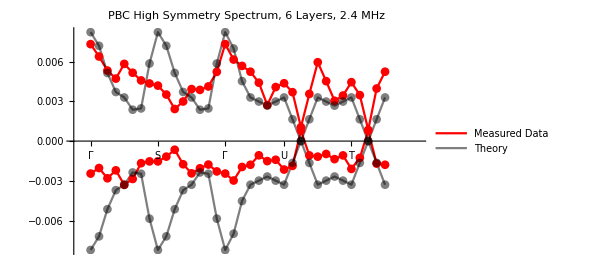
-Graphics-Laplacian Eigenvalues j_n

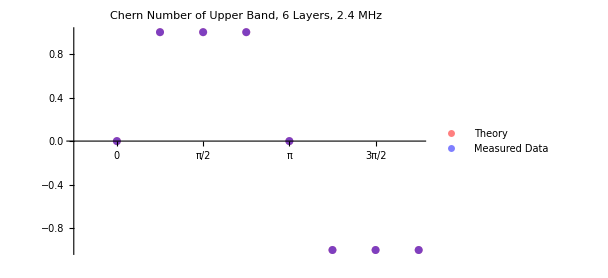
-Graphics-kxChern Number

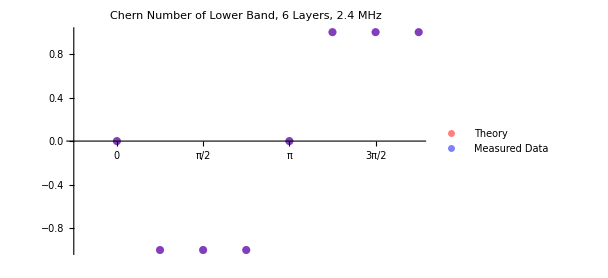
-Graphics-kxChern Number

-Graphics3D-

-Graphics3D-

```mathematica
SetOptions[$FrontEnd,ShowCellLabel->False]
(*High Symmetry Plot*)
Labeled[ListLinePlot[{evals[[1;;;;2]],evals[[2;;;;2]],LowerBandPathValsTheory*120.5,UpperBandPathValsTheory*120.5},Mesh->All,PlotLabel->"PBC High Symmetry Spectrum, "<>ToString[8+2*symmShift]<> " Layers, "<>ToString[Frequency/(10^6)]<>" MHz",PlotRange->{{-1,40},Automatic},PlotLegends->{"Measured Data",None,"Theory",None},PlotStyle->{Red,Red,{Black,Opacity[0.5]},{Black,Opacity[0.5]}},AxesOrigin->{-1,0},Ticks->{{{1,"Γ"},{5,"X"},{9,"S"},{13,"Y"},{17,"Γ"},{21+symmShift,"Z"},{25+symmShift,"U"},{29+symmShift,"R"},{33+symmShift,"T"},{37+symmShift,"Z"}},Automatic},ImageSize->450],{"","Laplacian Eigenvalues j_n"},{Bottom,Left},RotateLabel->True]

(*Chern Number*)
Grid[{{Labeled[ListPlot[{ChernTheoryV2Table[[;;,2]],ChernExperimentV2Table[[;;,1]]},PlotLabel->"Chern Number of Upper Band, "<>ToString[8+2*symmShift]<> " Layers, "<>ToString[Frequency/(10^6)]<>" MHz",PlotStyle->{{Opacity[0.5],Red},{Opacity[0.5],Blue}},PlotStyle->PointSize[Large],PlotLegends->{"Theory","Measured Data"},Ticks->{{{1,"0"},{3,"π/2"},{5,"π"},{7,"3π/2"}},Automatic},ImageSize->450],{"kx","Chern Number"},{Bottom,Left},RotateLabel->True]},{}},Frame->False,Spacings->{0,3}]

Grid[{{Labeled[ListPlot[{ChernTheoryV2Table[[;;,1]],ChernExperimentV2Table[[;;,2]]},PlotLabel->"Chern Number of Lower Band, "<>ToString[8+2*symmShift]<> " Layers, "<>ToString[Frequency/(10^6)]<>" MHz",PlotStyle->{{Opacity[0.5],Red},{Opacity[0.5],Blue}},PlotStyle->PointSize[Large],PlotLegends->{"Theory","Measured Data"},Ticks->{{{1,"0"},{3,"π/2"},{5,"π"},{7,"3π/2"}},Automatic},ImageSize->450],{"kx","Chern Number"},{Bottom,Left},RotateLabel->True]}},Frame->False,Spacings->{0,3}]


ListPlot3D[resultPerTotMeas[[NVertical/2+1]],PlotRange->Automatic,PlotStyle->{Orange,Green},ImageSize->Large,Mesh->All,AxesLabel->{"k_x","k_y",Rotate["Laplacian Eigenvalues j_n",90 Degree]},Ticks->{{0,π/2,π,3π/2,2π},{0,π/2,π,3π/2,2π},Automatic},BaseStyle->{FontSize->11},AspectRatio->Automatic,ViewPoint->{-5,-2.4,0.65},PlotLabel->"Measurement Bandstructure at "<>"kz = π"]


ListPlot3D[{Transpose[HcEigenvals[[;;,;;,NVertical/2+1,1]]],Transpose[HcEigenvals[[;;,;;,NVertical/2+1,2]]]},PlotRange->Automatic,PlotStyle->{Orange,Green},ImageSize->Large,Mesh->All,AxesLabel->{"k_x","k_y",Rotate["Hamiltonian Eigenvalues E_n",90 Degree]},Ticks->{{{1,0},{NVertical/4+1,π/2},{NVertical/2+1,π},{3NVertical/4+1,3π/2}},{{1,0},{NVertical/4+1,π/2},{NVertical/2+1,π},{3NVertical/4+1,3π/2}},Automatic},BaseStyle->{FontSize->11},AspectRatio->Automatic,ViewPoint->{-5,-2.4,0.65},PlotLabel->"Theoretical Bandstructure at "<>"kz = π"]
```

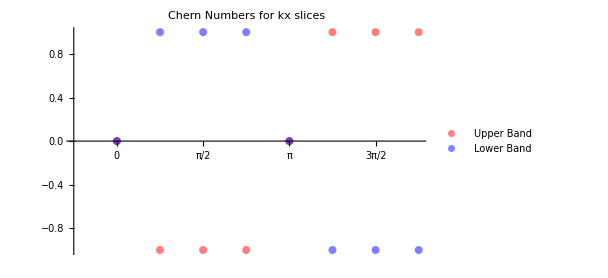
-Graphics-kxChern Number

```mathematica
Labeled[ListPlot[{ChernTheoryV2Table[[;;,1]],ChernTheoryV2Table[[;;,2]]},PlotLabel->"Chern Numbers for kx slices",PlotStyle->{{Opacity[0.5],Red},{Opacity[0.5],Blue}},PlotStyle->PointSize[Large],PlotLegends->{"Upper Band","Lower Band"},Ticks->{{{1,"0"},{3,"π/2"},{5,"π"},{7,"3π/2"}},Automatic},ImageSize->450],{"kx","Chern Number"},{Bottom,Left},RotateLabel->True]
```

```mathematica
LowerBandPathValsTheory=Table[Det[Hc[pathTheoretical[[i]]]],{i,1,Length[pathTheoretical]}];
UpperBandPathValsTheory=Table[-Det[Hc[pathTheoretical[[i]]]],{i,1,Length[pathTheoretical]}];

BandsTheory = Table[SortBy[120.5*{UpperBandPathValsTheory[[i]],LowerBandPathValsTheory[[i]]},Re],{i,1,Length[pathTheoretical]}];
BandsTheory//Dimensions
```

{36,2}

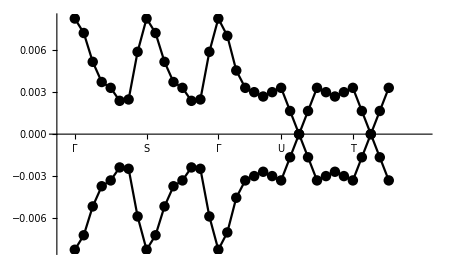
-Graphics-Hamiltonian Eigenvalues E_n

```mathematica
Labeled[ListLinePlot[{BandsTheory[[;;,1]],BandsTheory[[;;,2]]},Mesh->All,PlotRange->{{-1,40},Automatic},PlotStyle->{Black,Black},AxesOrigin->{-1,0},Ticks->{{{1,"Γ"},{5,"X"},{9,"S"},{13,"Y"},{17,"Γ"},{21+symmShift,"Z"},{25+symmShift,"U"},{29+symmShift,"R"},{33+symmShift,"T"},{37+symmShift,"Z"}},Automatic},ImageSize->450],{"","Hamiltonian Eigenvalues E_n"},{Bottom,Left},RotateLabel->True]
```